# Lesson 8: The Derivative as a Function

## Exercise 1 - Derivative of a Function

Find the derivative of the function and plot it on a graph:

```mathematica
f[x_]:=(1-3x)/(2+x)
```

```mathematica
D[f[x],x]
```

-(1-3 x)/(2+x)^2-3/(2+x)

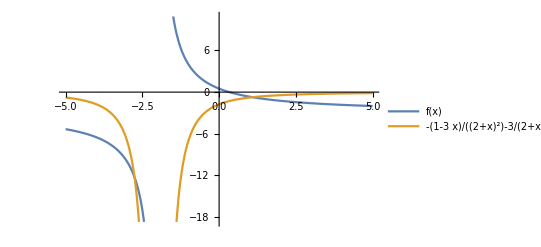

```mathematica
Plot[{f[x],Evaluate[D[f[x],x]]},{x,-5,5}, PlotLegends->"Expressions"]
```

## Exercise 2 - Differentiability

```mathematica
Clear[f];
```

```mathematica
f[x_]:=4CubeRoot[x]+2RealAbs[x-1]-
3 CubeRoot[x+2]^2
```

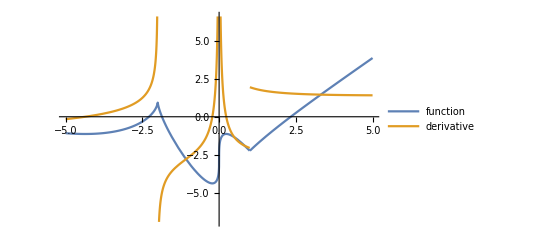

```mathematica
Plot[{f[x],Evaluate[D[f[x],x]]},{x,-5,5}, PlotLegends->{"function","derivative"}]
```

```mathematica
f'[0] //Quiet
```

ComplexInfinity

```mathematica
f'[1]//Quiet
```

Indeterminate

```mathematica
f'[-2]//Quiet
```

ComplexInfinity

## Exercise 3 - One-Sided Derivatives

Find the left- and right-hand derivatives of the following function at 10:

```mathematica
f[x_]:=CubeRoot[x-10]
```

```mathematica
Limit[DifferenceQuotient[f[x],{x,h}], h->0,
Direction->"FromBelow"]/.x->10
```

∞

```mathematica
Limit[DifferenceQuotient[f[x],{x,h}],h->0,
Direction->"FromAbove"]/.x->10 //Quiet
```

ComplexInfinity

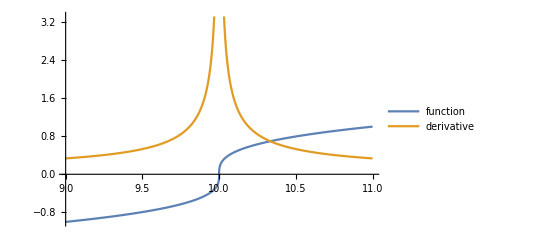

```mathematica
Plot[{f[x],Evaluate[D[f[x],x]]},{x,9,11},PlotLegends->
{"function","derivative"}]
```

## Exercise 4 - Higher Order Derivatives

Find and plot the fourth derivative of the following function:

```mathematica
f[x_]:=1/x
```

```mathematica
D[f[x],{x,4}]
```

24/x^5

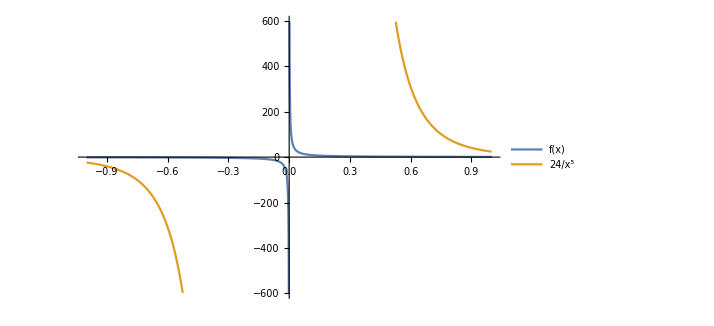

```mathematica
Plot[{f[x],Evaluate[D[f[x],{x,4}]]},{x,-1,1},
PlotLegends->"Expressions"]
```

## Exercise 5 - An Application from Physics

Find (and plot) the acceleration, jerk  and crackle of the following position function:

```mathematica
position[t_]:=(5-4t)/(3+t)
```

Acceleration - 2^nd derivative, jerk 3^rd derivative, and the crackle is the 5th:

```mathematica
{acceleration, jerk, crackle} = {D[position[t],{t,2}],
D[position[t],{t,3}],D[position[t],{t,5}]}
```

{(2 (5-4 t))/(3+t)^3+8/(3+t)^2,-(6 (5-4 t))/(3+t)^4-24/(3+t)^3,-(120 (5-4 t))/(3+t)^6-480/(3+t)^5}

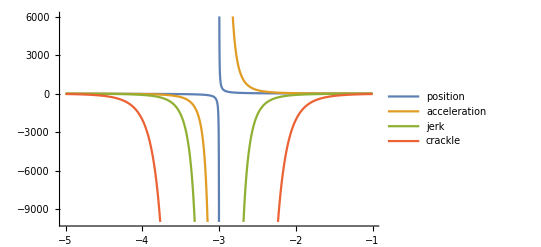

```mathematica
Plot[{position[t],acceleration,jerk, crackle},{t,-5,-1}, PlotLegends->
{"position","acceleration", "jerk","crackle"}]
```